```mathematica
suit ={"A",2,3,4,5,6,7,8,9,10,"J","Q","K"};
myDeck = Join[suit, suit, suit, suit];
myDeck = {#}&/@myDeck;
myDeck = myDeck/.{"J"->10,"Q"->10,"K"->10, {"A"}->{1, 11}};
```

```mathematica
deck
```

{{1,11},{2},{3},{4},{5},{6},{7},{8},{9},{10},{10},{10},{10},{1,11},{2},{3},{4},{5},{6},{7},{8},{9},{10},{10},{10},{10}}

```mathematica
twoCards = Subsets[deck,{2}];
```

```mathematica
twoCards[[1]]
```

{{1,11},{2}}

```mathematica
enumeratedAces = Tuples/@twoCards;
```

```mathematica
enumeratedTotal = Total[#,{2}]&/@enumeratedAces;
```

```mathematica
under21 = Select[#, #<=21&]&/@enumeratedTotal;
```

```mathematica
finalScore = Max/@under21;
```

```mathematica
Length[finalScore]
```

325

```mathematica
Count[finalScore, {}]
```

0

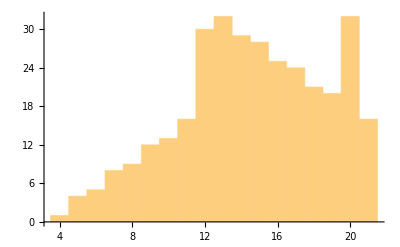

```mathematica
Histogram[finalScore]
```

```mathematica
drawCards[deck_,n_]:= Total[#,{2}]&/@(Tuples/@Subsets[deck,{n}])

bustCards[cards_, limit_]:=Max/@(Select[#, #<=limit&]&/@ cards)

regFail [cards_,minNeeded_,limit_]:=Count[bustCards[cards, limit],x_/;-1<x<minNeeded]/Length[cards]

regSuccess [cards_,minNeeded_,limit_]:=Count[bustCards[cards, limit],x_/;minNeeded<=x<limit]/Length[cards]

critFail [cards_,minNeeded_,limit_]:=
Count[bustCards[cards, limit],x_/;x<0]/Length[cards]

critSuccess[cards_,minNeeded_,limit_]:=Count[bustCards[cards, limit],limit]/Length[cards]

successVector[cards_,minNeeded_, limit_]:=
N[#,3]&/@{minNeeded - 1,
1-((minNeeded-2)*0.05),
minNeeded,
regSuccess[cards, minNeeded, limit]+critSuccess[cards, minNeeded, limit],
regFail[cards, minNeeded, limit]+critFail[cards, minNeeded, limit],
critSuccess[cards, minNeeded, limit],
critFail[cards, minNeeded, limit],
regSuccess[cards, minNeeded, limit],
regFail[cards, minNeeded, limit]
}

bustOdds [list_]:=N[Count[list,-∞]/Length[list],3]
```

```mathematica
drawTwo = drawCards[myDeck,2];
drawThree = drawCards[myDeck,3];
drawFour = drawCards[myDeck, 4];
drawFive = drawCards[myDeck, 5];
drawSix = drawCards[myDeck,6];
```

```mathematica
headings = {"Min. Roll","Roll Success","Min. Needed","Tot. Success","Tot. Fail","Crit. Success","Crit. Fail","Reg. Success", "Reg. Fail"};
```

```mathematica
Grid[Prepend[Table[successVector[drawTwo,n,21],{n,2,21}],headings],
{Background->{None,{{White,Lighter[Blend[{Blue,Green}],0.8]}}},Dividers->{{Gray,{LightGray},Gray}},Frame->True,Spacings->{2,{2,{0.7},2}}}]
```

Min. Roll | Roll Success | Min. Needed | Tot. Success | Tot. Fail | Crit. Success | Crit. Fail | Reg. Success | Reg. Fail
1. | 1. | 2. | 1. | 0 | 0.0483 | 0 | 0.952 | 0
2. | 0.95 | 3. | 1. | 0 | 0.0483 | 0 | 0.952 | 0
3. | 0.9 | 4. | 1. | 0 | 0.0483 | 0 | 0.952 | 0
4. | 0.85 | 5. | 0.995 | 0.00452 | 0.0483 | 0 | 0.947 | 0.00452
5. | 0.8 | 6. | 0.983 | 0.0166 | 0.0483 | 0 | 0.935 | 0.0166
6. | 0.75 | 7. | 0.967 | 0.0332 | 0.0483 | 0 | 0.919 | 0.0332
7. | 0.7 | 8. | 0.943 | 0.0573 | 0.0483 | 0 | 0.894 | 0.0573
8. | 0.65 | 9. | 0.914 | 0.086 | 0.0483 | 0 | 0.866 | 0.086
9. | 0.6 | 10. | 0.878 | 0.122 | 0.0483 | 0 | 0.83 | 0.122
10. | 0.55 | 11. | 0.837 | 0.163 | 0.0483 | 0 | 0.789 | 0.163
11. | 0.5 | 12. | 0.789 | 0.211 | 0.0483 | 0 | 0.741 | 0.211
12. | 0.45 | 13. | 0.695 | 0.305 | 0.0483 | 0 | 0.647 | 0.305
13. | 0.4 | 14. | 0.599 | 0.401 | 0.0483 | 0 | 0.551 | 0.401
14. | 0.35 | 15. | 0.51 | 0.49 | 0.0483 | 0 | 0.462 | 0.49
15. | 0.3 | 16. | 0.425 | 0.575 | 0.0483 | 0 | 0.377 | 0.575
16. | 0.25 | 17. | 0.348 | 0.652 | 0.0483 | 0 | 0.3 | 0.652
17. | 0.2 | 18. | 0.276 | 0.724 | 0.0483 | 0 | 0.228 | 0.724
18. | 0.15 | 19. | 0.211 | 0.789 | 0.0483 | 0 | 0.163 | 0.789
19. | 0.1 | 20. | 0.151 | 0.849 | 0.0483 | 0 | 0.103 | 0.849
20. | 0.05 | 21. | 0.0483 | 0.952 | 0.0483 | 0 | 0 | 0.952

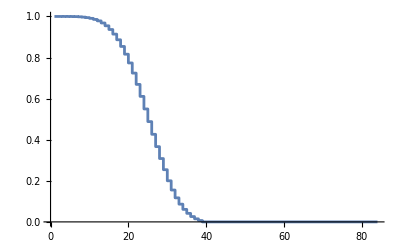

```mathematica
ListStepPlot[Table[bustOdds[bustCards[drawFour,n]],{n,2,84}]]
```

```mathematica
Table[n,{n,2,22}]
```

{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22}

```mathematica
drawSeven = drawCards[myDeck, 7];
```

```mathematica
bustOdds [list_]:=N[Count[list,-∞]/Length[list]]
```

```mathematica
bustOdds[drawSeven]
```

0.999088

```mathematica
N[399/400]
```

0.9975

Odds of busting on 21 with 7 drawn cards is 0.999088, or about 1/1000. For comparison, odds of NOT getting 20&20 with a disadvantaged roll is 0.9975.

## What about when you start to hit?

If you score less than a 12 on your first two cards, you should automatically hit, as it is impossible to bust. This needs to be taken into account, as what we really want is an odds table for the game state where the player has some chance of failing.

The way I go about doing this is a little different. I want to draw every permutation of three cards from the deck. I will sum the first two to get my starting number, and use the third number to calculate the value after hitting. I had previously used Mathematica’s “Subsets” function to draw my cards, but although that generates all possible sets, it does so assuming order does not matter. In this case, order does matter, because the set {A, 4, K} for example denotes hitting on a 15 and drawing a king, where as {A,K,4} denotes hitting on a 21 and drawing a 4. I don’t need all 6 permutations - {A,4,K} is equivalent to {4,A,K}, but it is less work to unnecessarily include them and make use of existing functions.

```mathematica
threeCards =MapIndexed[myDeck[[#]]&, Permutations[Range[52],{3}],{2}]
```

These next two lines are rather long and complicated. I have included an itemized breakdown at the end of this notebook. “finalTotal” denotes the final value after hitting once. “firstTwoTotal” is the total of the first two cards drawn - what is being hit on.

```mathematica
finalTotal = bustCards[Total[#,{2}]&/@(Tuples/@Transpose[{Total[#,{2}]&/@(Tuples/@threeCards[[All,;;2]]),threeCards[[All,3]]}]),21];
firstTwoTotal = bustCards[Total[#,{2}]&/@(Tuples/@threeCards[[All,;;2]]), 21];
```

bustOddsStartAtN: What is the likelihood of busting (going over 21) if you hit an initial hand with sums to “N”?
afterHitAvgValue: Assuming you don’t bust, what average value will you be left with after hitting once?

```mathematica
bustOddsStartAtN[firstTotal_,finalTotal_,beforeHit_]:=bustOdds[Pick[finalTotal,Map[#==beforeHit&,firstTotal]]]
afterHitAvgValue[firstTotal_,finalTotal_,beforeHit_]:=
N[
Mean[
Select[
Pick[finalTotal,Map[#==beforeHit&,firstTotal]],#>0&]
],3
]
```

```mathematica
Integer[Commonest[Pick[finalTotal,Map[#==7&,firstTwoTotal]]]]
```

Integer[{17}]

```mathematica
FromDigits[{17}]
```

17

```mathematica
Tally[Pick[finalTotal,Map[#==7&,firstTwoTotal]]]
```

{{18,256},{10,224},{11,224},{13,256},{14,256},{15,256},{16,256},{17,1024},{9,224},{12,224}}

```mathematica
1024/
```

8/25

```mathematica
N[8/25]
```

0.32

```mathematica
Grid[
Prepend[
Transpose[
{Range[4, 21],
Table[bustOddsStartAtN[firstTwoTotal, finalTotal,n],{n,4,21}],
Table[afterHitAvgValue[firstTwoTotal, finalTotal, n],{n,4,21}]}
], {"Start Tot.", "Odds of Bust", "Avg. Non-Bust Tot."}
],
{Background->{None,{{White,Lighter[Blend[{Blue,Green}],0.8]}}},Dividers->{{Gray,{LightGray},Gray}},Frame->True,Spacings->{2,{2,{0.7},2}}}
]
```

Start Tot. | Odds of Bust | Avg. Non-Bust Tot.
4 | 0 | 11.5
5 | 0 | 12.5
6 | 0 | 13.5
7 | 0 | 14.5
8 | 0 | 15.4
9 | 0 | 16.4
10 | 0 | 17.4
11 | 0 | 17.6
12 | 0.294 | 16.9
13 | 0.338 | 17.2
14 | 0.399 | 17.5
15 | 0.46 | 17.8
16 | 0.506 | 18.1
17 | 0.567 | 18.4
18 | 0.619 | 18.5
19 | 0.672 | 18.4
20 | 0.812 | 18.6
21 | 0 | 17.6

### Some Strange Results

```mathematica
Tally[Pick[threeCards[[All, ;;2]],Map[#==20&,firstTwoTotal]]]
```

{{{{1,11},{9}},800},{{{9},{1,11}},800},{{{10},{10}},12000}}

```mathematica
(12000*(50-4))/((12000+800+800)*50)
```

69/85

```mathematica
N[69/85]
```

0.811765

```mathematica
N[46/50]
```

0.92

This is a very interesting result! If you have a total of 20, and you hit, you only have an 81% chance of busting. Online tables show 92% odds, which at a glance seems more reasonable. What gives? Well, if you have A/9 combo, you have 20 but will never bust on the next turn (There are 1600 permutations of this). If you have any 10/10 combo (12,000 permutations of this), you will bust if your next card isn’t A. You drew two cards already, so 50 remain in the deck. 

Consider the 10/10. What are your odds of busting? Well, 46/50! That is our 92% from the internet. And we already know you have 0% odds from A/9.

```mathematica
1600/(12000+1600)*0+12000/(12000+1600)*0.92
```

0.811765

```mathematica
1600/(12000+1600)
```

2/17

```mathematica
N[2/17]
```

0.117647

```mathematica
N[2/17]
```

0.117647

```mathematica
N[2/15]
```

0.133333

### Rule of thumb

After you hit, you have a roughly 1/3 chance of going up by 10. Otherwise, your odds are evenly distributed. 

For example, below is a histogram of what results from hitting on a 7. You have 1024 ways to end up at 17, versus 3200 total outcomes. Further, the histogram shows that your other outcomes are roughly evenly distributed.

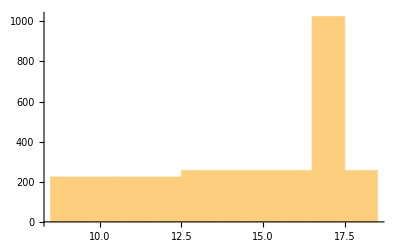

3200

0.32

```mathematica
Histogram[
Pick[finalTotal,Map[#==7&,firstTwoTotal]]]
Length@Pick[finalTotal,Map[#==7&,firstTwoTotal]]
N[1024/3200]
```

How to represent this for higher hitting at higher starting points can be a little ambiguous. For example, look at hitting on a 15 , shown below. What I’ve done throughout this notebook is “wrap” all values greater than 21 down to , which doesn’t show up on the histogram. Indeed, the most common outcome is a bust, which will occur 46% of the time.

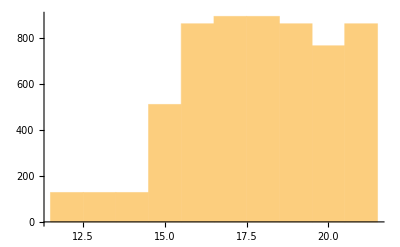

```mathematica
Histogram[
Pick[finalTotal,Map[#==15&,firstTwoTotal]]]
```

Let’s extend this analysis to all starting values. The function below tells me what fraction of the the final outcomes are equal to the most common outcome.

```mathematica
modeFrac[number_]:=
N[
(Count[#, FromDigits[Commonest[#]]]&@Pick[finalTotal,Map[#==number&,firstTwoTotal]])/
(Length[Pick[finalTotal,Map[#==number&,firstTwoTotal]]]),
3
]
```

In the table below...
Start Tot.: The total of our first two cards.
Aft. Hit Mode: The most common value occurring after drawing an additional card.
Odds of Aft. Hit Mode: What fraction of the final outcomes “Aft. Hit Mode” represents. 

Up until 12, the point at which we are no longer guaranteed  to be safe if we hit, we can expect to go up in value by 10, and we can expect that to occur about 1/3 of the time. After this point, we can expect to bust at best about 1/3 of the time, which gets worse as we go up in value (barring some funny business with valuing Aces at 1 or 11).

```mathematica
Grid[
Prepend[
Transpose@{Range[4, 21],
Table[Commonest[Pick[finalTotal,Map[#==n&,firstTwoTotal]]],{n,4,21}],
Table[modeFrac[n],{n,4,21}]},
{"Start Tot.", "Aft. Hit Mode","Odds. of Aft. Hit Mode"}
],
{Background->{None,{{White,Lighter[Blend[{Blue,Green}],0.8]}}},Dividers->{{Gray,{LightGray},Gray}},Frame->True,Spacings->{2,{2,{0.7},2}}}
]
```

Start Tot. | Aft. Hit Mode | Odds. of Aft. Hit Mode
4 | {14} | 0.32
5 | {15} | 0.32
6 | {16} | 0.32
7 | {17} | 0.32
8 | {18} | 0.32
9 | {19} | 0.32
10 | {20} | 0.32
11 | {21} | 0.32
12 | {-∞} | 0.294
13 | {-∞} | 0.338
14 | {-∞} | 0.399
15 | {-∞} | 0.46
16 | {-∞} | 0.506
17 | {-∞} | 0.567
18 | {-∞} | 0.619
19 | {-∞} | 0.672
20 | {-∞} | 0.812
21 | {21} | 0.3

It looks like we can expect about a 16, if we in

```mathematica
{N[Length@#/Length@firstTwoTotal], N[Mean@#]}&@Pick[finalTotal,Map[4<=#<=11&,firstTwoTotal]]
```

{0.211161,15.9571}

So, what’s the verdict here? Recall that our definition of success is “Get at least this number, but not over 21”.  We have about a 70% chance being at or above 12 on our first two cards, putting the players in the “danger zone” of possibly busting. The 30% of the time we aren’t in the Danger Zone, expect the players to hit to about a 16. At this point, they will have a 50% chance of going bust on the next hit. If they don’t bust, expect an 18. 

This is already complicated, and unfortunately only get’s worse... The longest possible hand you can have, and still be safe, is 8 cards long - {A, A, A, A, 2, 2, 2, 2} for a total of 12, just entering the Danger Zone. But your odds of busting noticeably higher than in the above table, 36% (44 cards remain, 12 of which have the value “10” which will bust you). So, you could continue through all these other hands, logging where they spit you out and compiling that into a final table with odds of 12-21 after perfect play.

```mathematica
1/Binomial[52, 8]
```

1/752538150

```mathematica
N[1/752538150]
```

1.32884×10^-9

## Monte Carlo

So, rather than directly calculating all of this, let’s do a monte carlo simulation.

Draw 8 cards at random, as 8 is the maximum number we can draw and just hit a value of 12.

```mathematica
draw = RandomChoice[myDeck, 8]
```

{{10},{4},{5},{1,11},{10},{9},{9},{5}}

Let’s use a fun edge case instead. A player wouldn’t hit a 21, but technically they could, and in this case that wouldn’t bust them.

```mathematica
draw = {{1, 11},{10}, {2}, {5}}
```

{{1,11},{10},{2},{5}}

This is the pattern of numbers we will sum over. The first list assumes we count the Ace as a 1, and the second assumes we count it as an 11.

```mathematica
Tuples@draw
```

{{1,10,2,5},{11,10,2,5}}

Calculate the cumulative sum - the result of drawing one more card.

```mathematica
Accumulate/@Tuples@draw
```

{{1,11,13,18},{11,21,23,28}}

We need to find the soonest possible location where we meet or surpass 12, as we have entered the Danger Zone where we may start busting. The below function gives all locations of numbers between (inclusive) 12 and 21, in {list, location in list} ordered pairs (Mathematica starts counting at one).

```mathematica
Position[Accumulate/@Tuples@draw,_?(12<=#<=21&)]
```

{{1,3},{1,4},{2,2}}

Choose ordered pair with the lowest second value, which corresponds to the fewest number of cards needed to enter the Danger Zone.

```mathematica
MinimalBy[Position[Accumulate/@Tuples@draw,_?(12<=#<=21&)],Last]
```

{{2,2}}

Get the value where we have entered the Danger Zone. This is the final result of a single simulated run!

```mathematica
Extract[Accumulate/@Tuples@draw, MinimalBy[Position[Accumulate/@Tuples@draw,_?(12<=#<=21&)],Last][[1]]]
```

21

```mathematica
monteFunc[draw_]:=Extract[Accumulate/@Tuples@draw, MinimalBy[Position[Accumulate/@Tuples@draw,_?(12<=#<=21&)],Last][[1]]]
```

Here is how we would do a single run with a random draw of 8 cards.

```mathematica
monteFunc[RandomChoice[myDeck, 8]]
```

20

And here is how we generate our final data set.

```mathematica
monteData = Table[monteFunc[RandomChoice[myDeck, 8]],{n,1,1000000}];
```

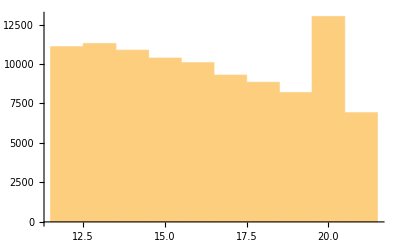

```mathematica
Histogram[monteData]
```

```mathematica
13010/100000
```

1301/10000

```mathematica
N[1301/10000]
```

0.1301

```mathematica
fracMatch[value_]:=N[Count[monteData,_?(#>=value&)]/Length[monteData],3]
```

```mathematica
Grid[
Prepend[
Transpose@{Range[12, 21],
Table[fracMatch[n],{n, 12, 21}]},
{"Get at least", "Odds"}
],
{Background->{None,{{White,Lighter[Blend[{Blue,Green}],0.8]}}},Dividers->{{Gray,{LightGray},Gray}},Frame->True,Spacings->{2,{2,{0.7},2}}}
]
```

Get at least | Odds
12 | 1.
13 | 0.889
14 | 0.776
15 | 0.667
16 | 0.563
17 | 0.463
18 | 0.37
19 | 0.281
20 | 0.199
21 | 0.0692

Start Tot. | Odds of Bust | Avg. Non-Bust Tot.
4 | 0 | 11.5
5 | 0 | 12.5
6 | 0 | 13.5
7 | 0 | 14.5
8 | 0 | 15.4
9 | 0 | 16.4
10 | 0 | 17.4
11 | 0 | 17.6
12 | 0.294 | 16.9
13 | 0.338 | 17.2
14 | 0.399 | 17.5
15 | 0.46 | 17.8
16 | 0.506 | 18.1
17 | 0.567 | 18.4
18 | 0.619 | 18.5
19 | 0.672 | 18.4
20 | 0.812 | 18.6
21 | 0 | 17.6

And there we have it! Our (approximate) riskless play. 100% chance of getting at least a 12, about a 50% chance of getting at least a 16 or 17, and a 7% chance of getting a perfect 21. Odds of blackjack, about 5%.

If a DM asks for a 16, you have a 56% chance of getting it right off the bat. But the other 44% of the time, you’re gonna have to hit at least once, busting you about 50% of the time after that first hit.

So... Where does that leave us? I’d use this above-table to (without telling the players), set baseline assuming perfectly safe play. This is basically your dice roll. On a soft failure (not busting), they don’t get what they want, but it isn’t awful. If they do push their luck, hit, and bust, something pretty bad happens.

```mathematica
Flatten[Accumulate/@Tuples@draw]
```

{3,6,7,17,27,37,47,51,3,6,17,27,37,47,57,61}

```mathematica
Position[Accumulate/@Tuples@draw,_?(12<=#<=21&)]
```

{{1,3},{1,4},{2,2}}

```mathematica
First@MinimalBy[Position[Accumulate/@Tuples@draw,_?(12<=#<=21&)],Last]
```

{2,2}

```mathematica
Extract[Accumulate/@Tuples@draw, MinimalBy[Position[Accumulate/@Tuples@draw,_?(12<=#<=21&)],Last][[1]]]
```

21

```mathematica
(Accumulate/@Tuples@draw)[[2,2]]
```

21

```mathematica
{{2, 2}}[[0]]
```

List

```mathematica
Subsets[myDeck,{3}]
```

```mathematica
Accumulate[%139]
```

Accumulate::tdlen: Objects of unequal length in {{2},{7},{8},{1,11},{5},{9},{4},{1,11}} cannot be added.

Accumulate[{{2},{7},{8},{1,11},{5},{9},{4},{1,11}}]

```mathematica
Tuples/@%
```

Tuples::normal: Nonatomic expression expected at position {1,1} in Tuples[{2}].

Tuples::normal: Nonatomic expression expected at position {1,1} in Tuples[{7}].

Tuples::normal: Nonatomic expression expected at position {1,1} in Tuples[{8}].

General::stop: Further output of Tuples::normal will be suppressed during this calculation.

{Tuples[{2}],Tuples[{7}],Tuples[{8}],Tuples[{1,11}],Tuples[{5}],Tuples[{9}],Tuples[{4}],Tuples[{1,11}]}

```mathematica
16/44
```

4/11

```mathematica
N[4/11]
```

0.363636

```mathematica
Length@final
```

Some of that got a little complicated, so I copy the parts where I go step-by-step here

```mathematica
threeCards[[All,;;2]]
```

```mathematica
Total[#,{2}]&/@(Tuples/@threeCards[[All,;;2]])
```

```mathematica
Transpose[{Total[#,{2}]&/@(Tuples/@threeCards[[All,;;2]]),threeCards[[All,3]]}]
```

```mathematica
Tuples/@Transpose[{Total[#,{2}]&/@(Tuples/@threeCards[[All,;;2]]),threeCards[[All,3]]}]
```

```mathematica
Total[#,{2}]&/@(Tuples/@Transpose[{Total[#,{2}]&/@(Tuples/@threeCards[[All,;;2]]),threeCards[[All,3]]}])
```

How many Ace & 9 Combinations?

```mathematica
Binomial[13,1]*Binomial[12,1]*Binomial[4,1]*Binomial[4,1]
```

2496

How many 10 & 10 combinations?

```mathematica
Binomial[13,4]Binomial[]
```

```mathematica
Binomial[13,1]
```

13

```mathematica
Binomial[4,4]
```

1

```mathematica
13*13
```

169

```mathematica
N[Mean[thirdAtN]]
```

-∞

```mathematica
N[25/2]
```

12.5

```mathematica
N[Count[thirdAtN,x_/;x<0]/Length[thirdAtN]]
```

0.811765

```mathematica
N[27/80]
```

0.3375

```mathematica
N[228/775]
```

0.294194

```mathematica
critFail[thirdAtN,0,21]
```

Select::normal: Nonatomic expression expected at position 1 in Select[14,#1≤21&].

Select::normal: Nonatomic expression expected at position 1 in Select[15,#1≤21&].

Select::normal: Nonatomic expression expected at position 1 in Select[16,#1≤21&].

General::stop: Further output of Select::normal will be suppressed during this calculation.

228/775

```mathematica
Length[Pick[finalTotal,Map[#==12&,firstTwoTotal]]]
```

12400

```mathematica
Tuples[{{"A"},{1, 2}}]
```

{{A,1},{A,2}}

```mathematica
Join[Subsets[myDeck,{1}]
```

{{{1,11}},{{2}},{{3}},{{4}},{{5}},{{6}},{{7}},{{8}},{{9}},{{10}},{{10}},{{10}},{{10}},{{1,11}},{{2}},{{3}},{{4}},{{5}},{{6}},{{7}},{{8}},{{9}},{{10}},{{10}},{{10}},{{10}},{{1,11}},{{2}},{{3}},{{4}},{{5}},{{6}},{{7}},{{8}},{{9}},{{10}},{{10}},{{10}},{{10}},{{1,11}},{{2}},{{3}},{{4}},{{5}},{{6}},{{7}},{{8}},{{9}},{{10}},{{10}},{{10}},{{10}}}

```mathematica
Length[drawFive]
```

2598960

```mathematica
Count[drawFive,-∞]
```

2458988

```mathematica
Subsets
```

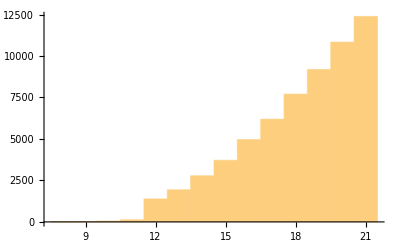

```mathematica
Histogram[drawCards[myDeck, 4]]
```

```mathematica
DeleteElements[myDeck,1->{{1, 11}, {1, 11}}]
```

{{2},{3},{4},{5},{6},{7},{8},{9},{10},{10},{10},{10},{2},{3},{4},{5},{6},{7},{8},{9},{10},{10},{10},{10},{1,11},{2},{3},{4},{5},{6},{7},{8},{9},{10},{10},{10},{10},{1,11},{2},{3},{4},{5},{6},{7},{8},{9},{10},{10},{10},{10}}

```mathematica
drawTwo
```

{{3,13},{4,14},{5,15},{6,16},{7,17},{8,18},{9,19},{10,20},{11,21},{11,21},{11,21},{11,21},{2,12,12,22},{3,13},{4,14},{5,15},{6,16},{7,17},{8,18},{9,19},{10,20},{11,21},{11,21},{11,21},{11,21},{2,12,12,22},{3,13},{4,14},{5,15},{6,16},{7,17},{8,18},{9,19},{10,20},{11,21},{11,21},{11,21},{11,21},{2,12,12,22},{3,13},{4,14},{5,15},{6,16},{7,17},{8,18},{9,19},{10,20},{11,21},{11,21},{11,21},{11,21},{5},{6},{7},{8},{9},{10},{11},{12},{12},{12},{12},{3,13},{4},{5},{6},{7},{8},{9},{10},{11},{12},{12},{12},{12},{3,13},{4},{5},{6},{7},{8},{9},{10},{11},{12},{12},{12},{12},{3,13},{4},{5},{6},{7},{8},{9},{10},{11},{12},{12},{12},{12},{7},{8},{9},{10},{11},{12},{13},{13},{13},{13},{4,14},{5},{6},{7},{8},{9},{10},{11},{12},{13},{13},{13},{13},{4,14},{5},{6},{7},{8},{9},{10},{11},{12},{13},{13},{13},{13},{4,14},{5},{6},{7},{8},{9},{10},{11},{12},{13},{13},{13},{13},{9},{10},{11},{12},{13},{14},{14},{14},{14},{5,15},{6},{7},{8},{9},{10},{11},{12},{13},{14},{14},{14},{14},{5,15},{6},{7},{8},{9},{10},{11},{12},{13},{14},{14},{14},{14},{5,15},{6},{7},{8},{9},{10},{11},{12},{13},{14},{14},{14},{14},{11},{12},{13},{14},{15},{15},{15},{15},{6,16},{7},{8},{9},{10},{11},{12},{13},{14},{15},{15},{15},{15},{6,16},{7},{8},{9},{10},{11},{12},{13},{14},{15},{15},{15},{15},{6,16},{7},{8},{9},{10},{11},{12},{13},{14},{15},{15},{15},{15},{13},{14},{15},{16},{16},{16},{16},{7,17},{8},{9},{10},{11},{12},{13},{14},{15},{16},{16},{16},{16},{7,17},{8},{9},{10},{11},{12},{13},{14},{15},{16},{16},{16},{16},{7,17},{8},{9},{10},{11},{12},{13},{14},{15},{16},{16},{16},{16},{15},{16},{17},{17},{17},{17},{8,18},{9},{10},{11},{12},{13},{14},{15},{16},{17},{17},{17},{17},{8,18},{9},{10},{11},{12},{13},{14},{15},{16},{17},{17},{17},{17},{8,18},{9},{10},{11},{12},{13},{14},{15},{16},{17},{17},{17},{17},{17},{18},{18},{18},{18},{9,19},{10},{11},{12},{13},{14},{15},{16},{17},{18},{18},{18},{18},{9,19},{10},{11},{12},{13},{14},{15},{16},{17},{18},{18},{18},{18},{9,19},{10},{11},{12},{13},{14},{15},{16},{17},{18},{18},{18},{18},{19},{19},{19},{19},{10,20},{11},{12},{13},{14},{15},{16},{17},{18},{19},{19},{19},{19},{10,20},{11},{12},{13},{14},{15},{16},{17},{18},{19},{19},{19},{19},{10,20},{11},{12},{13},{14},{15},{16},{17},{18},{19},{19},{19},{19},{20},{20},{20},{11,21},{12},{13},{14},{15},{16},{17},{18},{19},{20},{20},{20},{20},{11,21},{12},{13},{14},{15},{16},{17},{18},{19},{20},{20},{20},{20},{11,21},{12},{13},{14},{15},{16},{17},{18},{19},{20},{20},{20},{20},{20},{20},{11,21},{12},{13},{14},{15},{16},{17},{18},{19},{20},{20},{20},{20},{11,21},{12},{13},{14},{15},{16},{17},{18},{19},{20},{20},{20},{20},{11,21},{12},{13},{14},{15},{16},{17},{18},{19},{20},{20},{20},{20},{20},{11,21},{12},{13},{14},{15},{16},{17},{18},{19},{20},{20},{20},{20},{11,21},{12},{13},{14},{15},{16},{17},{18},{19},{20},{20},{20},{20},{11,21},{12},{13},{14},{15},{16},{17},{18},{19},{20},{20},{20},{20},{11,21},{12},{13},{14},{15},{16},{17},{18},{19},{20},{20},{20},{20},{11,21},{12},{13},{14},{15},{16},{17},{18},{19},{20},{20},{20},{20},{11,21},{12},{13},{14},{15},{16},{17},{18},{19},{20},{20},{20},{20},{3,13},{4,14},{5,15},{6,16},{7,17},{8,18},{9,19},{10,20},{11,21},{11,21},{11,21},{11,21},{2,12,12,22},{3,13},{4,14},{5,15},{6,16},{7,17},{8,18},{9,19},{10,20},{11,21},{11,21},{11,21},{11,21},{2,12,12,22},{3,13},{4,14},{5,15},{6,16},{7,17},{8,18},{9,19},{10,20},{11,21},{11,21},{11,21},{11,21},{5},{6},{7},{8},{9},{10},{11},{12},{12},{12},{12},{3,13},{4},{5},{6},{7},{8},{9},{10},{11},{12},{12},{12},{12},{3,13},{4},{5},{6},{7},{8},{9},{10},{11},{12},{12},{12},{12},{7},{8},{9},{10},{11},{12},{13},{13},{13},{13},{4,14},{5},{6},{7},{8},{9},{10},{11},{12},{13},{13},{13},{13},{4,14},{5},{6},{7},{8},{9},{10},{11},{12},{13},{13},{13},{13},{9},{10},{11},{12},{13},{14},{14},{14},{14},{5,15},{6},{7},{8},{9},{10},{11},{12},{13},{14},{14},{14},{14},{5,15},{6},{7},{8},{9},{10},{11},{12},{13},{14},{14},{14},{14},{11},{12},{13},{14},{15},{15},{15},{15},{6,16},{7},{8},{9},{10},{11},{12},{13},{14},{15},{15},{15},{15},{6,16},{7},{8},{9},{10},{11},{12},{13},{14},{15},{15},{15},{15},{13},{14},{15},{16},{16},{16},{16},{7,17},{8},{9},{10},{11},{12},{13},{14},{15},{16},{16},{16},{16},{7,17},{8},{9},{10},{11},{12},{13},{14},{15},{16},{16},{16},{16},{15},{16},{17},{17},{17},{17},{8,18},{9},{10},{11},{12},{13},{14},{15},{16},{17},{17},{17},{17},{8,18},{9},{10},{11},{12},{13},{14},{15},{16},{17},{17},{17},{17},{17},{18},{18},{18},{18},{9,19},{10},{11},{12},{13},{14},{15},{16},{17},{18},{18},{18},{18},{9,19},{10},{11},{12},{13},{14},{15},{16},{17},{18},{18},{18},{18},{19},{19},{19},{19},{10,20},{11},{12},{13},{14},{15},{16},{17},{18},{19},{19},{19},{19},{10,20},{11},{12},{13},{14},{15},{16},{17},{18},{19},{19},{19},{19},{20},{20},{20},{11,21},{12},{13},{14},{15},{16},{17},{18},{19},{20},{20},{20},{20},{11,21},{12},{13},{14},{15},{16},{17},{18},{19},{20},{20},{20},{20},{20},{20},{11,21},{12},{13},{14},{15},{16},{17},{18},{19},{20},{20},{20},{20},{11,21},{12},{13},{14},{15},{16},{17},{18},{19},{20},{20},{20},{20},{20},{11,21},{12},{13},{14},{15},{16},{17},{18},{19},{20},{20},{20},{20},{11,21},{12},{13},{14},{15},{16},{17},{18},{19},{20},{20},{20},{20},{11,21},{12},{13},{14},{15},{16},{17},{18},{19},{20},{20},{20},{20},{11,21},{12},{13},{14},{15},{16},{17},{18},{19},{20},{20},{20},{20},{3,13},{4,14},{5,15},{6,16},{7,17},{8,18},{9,19},{10,20},{11,21},{11,21},{11,21},{11,21},{2,12,12,22},{3,13},{4,14},{5,15},{6,16},{7,17},{8,18},{9,19},{10,20},{11,21},{11,21},{11,21},{11,21},{5},{6},{7},{8},{9},{10},{11},{12},{12},{12},{12},{3,13},{4},{5},{6},{7},{8},{9},{10},{11},{12},{12},{12},{12},{7},{8},{9},{10},{11},{12},{13},{13},{13},{13},{4,14},{5},{6},{7},{8},{9},{10},{11},{12},{13},{13},{13},{13},{9},{10},{11},{12},{13},{14},{14},{14},{14},{5,15},{6},{7},{8},{9},{10},{11},{12},{13},{14},{14},{14},{14},{11},{12},{13},{14},{15},{15},{15},{15},{6,16},{7},{8},{9},{10},{11},{12},{13},{14},{15},{15},{15},{15},{13},{14},{15},{16},{16},{16},{16},{7,17},{8},{9},{10},{11},{12},{13},{14},{15},{16},{16},{16},{16},{15},{16},{17},{17},{17},{17},{8,18},{9},{10},{11},{12},{13},{14},{15},{16},{17},{17},{17},{17},{17},{18},{18},{18},{18},{9,19},{10},{11},{12},{13},{14},{15},{16},{17},{18},{18},{18},{18},{19},{19},{19},{19},{10,20},{11},{12},{13},{14},{15},{16},{17},{18},{19},{19},{19},{19},{20},{20},{20},{11,21},{12},{13},{14},{15},{16},{17},{18},{19},{20},{20},{20},{20},{20},{20},{11,21},{12},{13},{14},{15},{16},{17},{18},{19},{20},{20},{20},{20},{20},{11,21},{12},{13},{14},{15},{16},{17},{18},{19},{20},{20},{20},{20},{11,21},{12},{13},{14},{15},{16},{17},{18},{19},{20},{20},{20},{20},{3,13},{4,14},{5,15},{6,16},{7,17},{8,18},{9,19},{10,20},{11,21},{11,21},{11,21},{11,21},{5},{6},{7},{8},{9},{10},{11},{12},{12},{12},{12},{7},{8},{9},{10},{11},{12},{13},{13},{13},{13},{9},{10},{11},{12},{13},{14},{14},{14},{14},{11},{12},{13},{14},{15},{15},{15},{15},{13},{14},{15},{16},{16},{16},{16},{15},{16},{17},{17},{17},{17},{17},{18},{18},{18},{18},{19},{19},{19},{19},{20},{20},{20},{20},{20},{20}}

```mathematica
Tuples[suit]
```

Tuples::normal: Nonatomic expression expected at position {1,1} in Tuples[{A,2,3,4,5,6,7,8,9,10,«3»}].

```mathematica
Tuples[Tuples[deck,2]]
```

Tuples::toomany: The length of the output of Tuples[{{{1,11},{1,11}},{{1,11},{2}},{{1,11},{3}},{{1,11},{4}},{{1,11},{5}},{{1,11},{6}},{{1,11},{7}},{{1,11},{8}},{{1,11},{9}},{{1,11},{10}},«2694»}] should be a machine integer.

```mathematica
Total[{{1, 11},{1,11}, 10}]
```

{12,32}

```mathematica
Tuples[{{1,11},{10}}]
```

{{1,10},{11,10}}

```mathematica
List[10]
```

{10}